## Notebook Setups

```mathematica
$HistoryLength=0;
```

#### Formatting

```mathematica
LMR="Latin Modern Roman";
Av="Avenir";
Ar="Arial";
TNR="Times New Roman";
BOS="Bookman Old Style";
fontfam=LMR;
nmbrsize=14;
labelsize=12;
episize=12;
framethick=0.003;
thick=0.005;
fs=Directive[{Black,FontFamily->fontfam,FontSize->nmbrsize,Thickness[framethick]}];
```

#### Import

```mathematica
importSetup[paramNames_,paramTypes_,dir_,setupFilename_]:=AssociationThread[paramNames->Import[dir<>setupFilename,"Binary","DataFormat"->paramTypes][[1]]];
```

```mathematica
importReal64MultiList[dir_,template_]:=Module[{filenameTemplate,depth,dimensions,imported},
filenameTemplate=StringTemplate[template];
depth=StringCount[template,"``"];
dimensions=(Length[FileNames[#,dir,1]]&)@*(TemplateApply[filenameTemplate,Table[If[i==#,"*",0],{i,depth}]]&)/@Range[depth];
imported=Array[Import[dir<>filenameTemplate[##],"Real64"]&,dimensions,ConstantArray[0,depth]];
{dimensions,imported}
];
```

#### Intermediaries

```mathematica
computekSpectrumPoints[setup_]:=Module[{n=setup[["N"]],L=setup[["L"]]},(2π)/L √Range[0,3(n/2)^2]];
```

```mathematica
computeBins[setup_]:=Module[{n=setup[["N"]],L=setup[["L"]]},BinLists[Range[0,3(setup["N"]/2)^2],{Table[k^2,{k,0,setup["N"]/2}]}]];
computeBinnedkSpectrumPoints[setup_]:=Module[{n=setup[["N"]],L=setup[["L"]]},(2π)/setup["L"] Range[0,setup["N"]/2-1]];
```

```mathematica
(*computeMultiplicityList[n_?NumberQ]:=Sort@Tally@Flatten@Array[(#1^2+#2^2+#3^2&),{n,n,n},{-n/2+1,-n/2+1,-n/2+1}];
computeMultiplicityList[setup_]:=computeMultiplicityList[setup[["N"]]];*)
```

```mathematica
computeMultiplicityList[n_?NumberQ]:={Range[0,3(n/2)^2],BinCounts[Flatten@Array[(#1^2+#2^2+#3^2&),{n,n,n},{-n/2+1,-n/2+1,-n/2+1}],{0,3(n/2)^2+1,1}]}ᵀ;
computeMultiplicityList[setup_]:=computeMultiplicityList[setup[["N"]]];
```

```mathematica
ClearAll[intermediaries];
intermediaries=CreateDataStructure["HashTable"];
```

```mathematica
computeIntermediaries[setup_]:=Module[{kSpectrumPoints,multiplicityList,indicesOfNonZeroMultiplicity,nonZeroMultiplicity,bins,binnedkSpectrumPoints,intermediariesForSetup},
kSpectrumPoints=computekSpectrumPoints[setup];
bins=computeBins[setup];
binnedkSpectrumPoints=computeBinnedkSpectrumPoints[setup];
multiplicityList=computeMultiplicityList[setup];
(*indicesOfNonZeroMultiplicity=multiplicityListᵀ[[1]];
nonZeroMultiplicity=multiplicityListᵀ[[2]];*)
intermediariesForSetup["kSpectrumPoints"]=kSpectrumPoints;
intermediariesForSetup["bins"]=bins;
intermediariesForSetup["binnedkSpectrumPoints"]=binnedkSpectrumPoints;
intermediariesForSetup["multiplicityList"]=multiplicityList;
(*intermediariesForSetup["indicesOfNonZeroMultiplicity"]=indicesOfNonZeroMultiplicity;
intermediariesForSetup["nonZeroMultiplicity"]=nonZeroMultiplicity;*)
intermediaries["Insert",Hash[setup]->intermediariesForSetup];
];
```

```mathematica
getIntermediary[setup_,name_]:=If[MissingQ[intermediaries["Lookup",Hash[setup]]],
computeIntermediaries[setup];intermediaries["Lookup",Hash[setup]][name],
intermediaries["Lookup",Hash[setup]][name]];
```

#### Spectrums

```mathematica
ClearAll[computeSmoothedPowerSpectrum,computeBinnedSpectrum];
```

```mathematica
computeBinnedSpectrum[setup_,spectrum_]:=Module[{
kSpectrumPoints=getIntermediary[setup,"kSpectrumPoints"],
bins=getIntermediary[setup,"bins"],
binnedkSpectrumPoints=getIntermediary[setup,"binnedkSpectrumPoints"]},
{binnedkSpectrumPoints,Total[spectrum[[#+1]]]&/@bins}ᵀ
];
```

```mathematica
computeBinnedSpectrum2[setup_,spectrum_]:=Module[{
kSpectrumPoints=getIntermediary[setup,"kSpectrumPoints"],
(*bins=({#}&/@Cases[_Integer?(#<=80&)][getIntermediary[setup,"multiplicityList"][[All,1]]])~Join~getIntermediary[setup,"bins"][[10;;-1]],*)
(*bins=BinLists[Range[0,3(setup["N"]/2)^2],{Table[k^2,{k,0,setup["N"]/2,0.5}]}],*)
bins=BinLists[Range[1,3(setup["N"]/2)^2],{Table[Exp[lnk]^2,{lnk,0,Log[setup["N"]/2],0.06}]}],
binnedkSpectrumPoints},
bins=Cases[_?(Total[getIntermediary[setup,"multiplicityList"][[#+1,2]]]>0&)][bins];
binnedkSpectrumPoints=(2π)/setup["L"] √bins[[All,1]];
{binnedkSpectrumPoints,(1/Total[getIntermediary[setup,"multiplicityList"][[#+1,2]]] Total[spectrum[[#+1]]]&)/@bins}ᵀ
];
```

```mathematica
(*tempBins=({#}&/@Cases[_Integer?(#<=80&)][getIntermediary[setup,"multiplicityList"][[All,1]]])~Join~getIntermediary[setup,"bins"][[10;;-1]];*)
```

```mathematica
(*BinLists[Range[1,3(setup["N"]/2)^2],{Table[Exp[lnk]^2,{lnk,0,Log[setup["N"]/2],0.015}]}][[1;;200]];*)
```

```mathematica
(*Total[getIntermediary[setup,"multiplicityList"][[#+1,2]]]&/@tempBins[[1;;20]]*)
```

#### Temporary tests on kfs fitting

```mathematica
(*multiplicityAssociation=Association[(#[[1]]->#[[2]]&)/@getIntermediary[setup,"multiplicityList"]];*)
```

```mathematica
(*multiplicityAssociation/@tempBins[[197]]*)
```

```mathematica
(*Total[multiplicityAssociation/@tempBins[[197]]]*)
```

```mathematica
(*(6*√1+12*√2+8*√3)/(6+12+8)//N*)
```

```mathematica
(*δSpectrumList[[1]]//Dimensions
3*(setup["N"]/2)^2+1*)
```

```mathematica
(*δSpectrumList[[1]][[1;;50]]*)
```

```mathematica
(*getIntermediary[setup,"kSpectrumPoints"]//Dimensions
getIntermediary[setup,"kSpectrumPoints"][[1;;50]]*)
```

## Plotting 3D numerical results for single evolution (radiation domination)

#### Load data

```mathematica
(*dir=NotebookDirectory[]<>"output/FS_Without_Gravity/";*)
dir=NotebookDirectory[]<>"output/Growth_and_FS_2/";
paramNames=Import[dir<>"paramNames.txt","List"];
paramTypes=Import[dir<>"paramTypes.txt","List"];
setup=importSetup[paramNames,paramTypes,dir,"param.dat"]
```

<|N→384,L→307.2,m→1.,lambda→0.,f_a→10.,k_ast→1.,k_Psi→1.,varphi_std_dev→1.,Psi_std_dev→0.02,a1→1.,H1→0.05,t1→10.,t_start→10.,t_end→36000.,t_interval→49.99,delta_t→0.5,M→128|>

```mathematica
{{numSnapshots},ρSpectrumList}=importReal64MultiList[dir,"rho_spectrum_``.dat"];
(*ρSpectrumBinnedList=computeBinnedSpectrum[setup,#]&/@ρSpectrumList;
ρPowerSpectrumList=Map[{#[[1]],(((2π)/L)^-1 1/n^6/.{n->setup["N"],L->setup["L"]})#[[1]]#[[2]]}&,ρSpectrumBinnedList,{-2}];*)
```

```mathematica
δSpectrumList=ρSpectrumList/(ρSpectrumList[[All,1]]/n^6/.n->setup["N"]);
δPowerSpectrumList=Map[{#[[1]],(((2π)/setup["L"])^-1 1/setup["N"]^6)#[[1]]#[[2]]}&,computeBinnedSpectrum[setup,#]&/@δSpectrumList,{-2}];
```

```mathematica
δPowerSpectrum2List=Map[{#[[1]],4π(#[[1]])^3/(2π/setup["L"])^3(#[[2]])/setup["N"]^6}&,computeBinnedSpectrum2[setup,#]&/@δSpectrumList,{-2}];
```

```mathematica
φPlusSpectrumList=importReal64MultiList[dir,"varphi_plus_spectrum_``.dat"][[2]];
φPlusPowerSpectrumList=Map[{#[[1]],(((2π)/setup["L"])^-1 1/setup["N"]^6)#[[1]]#[[2]]}&,computeBinnedSpectrum[setup,#]&/@φPlusSpectrumList,{-2}];
```

```mathematica
(*ListLogLogPlot[δPowerSpectrum2List[[{1,-1}]],PlotRange->{All,{10^-4,10}},Joined->True,ImageSize->Large]*)
```

```mathematica
(*ListLogLogPlot[δPowerSpectrum2List[[{1,-1}]],PlotRange->{All,{10^-4,10}},Joined->True,ImageSize->Large]*)
```

```mathematica
(*ListLogLogPlot[{δPowerSpectrumList[[-1]],WKBδPowerSpectrumList[[-1]]},PlotRange->{All,{10^-4,10}},Joined->True]*)
```

```mathematica
(*numSnapshots=φPlusPowerSpectrumList//Length;*)
```

```mathematica
(*ΨSpectrumList={importReal64MultiList[dir,"initial_Psi_spectrum.dat"][[2]]};
ΨSpectrumBinnedList=computeBinnedSpectrum[setup,#]&/@ΨSpectrumList;
ΨPowerSpectrumList=Map[{#[[1]],(((2π)/L)^-1 1/n^6/.{n->setup["N"],L->setup["L"]})#[[1]]#[[2]]}&,ΨSpectrumBinnedList,{-2}];*)
```

```mathematica
(*{{numSnapshots},dtρSpectrumList}=importReal64MultiList[dir,"dot_rho_spectrum_``.dat"];
dtρSpectrumBinnedList=computeBinnedSpectrum[setup,#]&/@dtρSpectrumList;
dtρPowerSpectrumList=Map[{#[[1]],(((2π)/L)^-1 1/n^6/.{n->setup["N"],L->setup["L"]})#[[1]]#[[2]]}&,dtρSpectrumBinnedList,{-2}];*)
```

```mathematica
(*dtδSpectrumList=dtρSpectrumList/(ρSpectrumList[[All,1]]/n^6/.n->setup["N"]);
dtδSpectrumBinnedLis10.5*((30^2-1)1/(2*0.05))/(8000-5)/5t=computeBinnedSpectrum[setup,#]&/@dtδSpectrumList;
dtδPowerSpectrumList=Map[{#[[1]],(((2π)/L)^-1 1/n^6/.{n->setup["N"],L->setup["L"]})#[[1]]#[[2]]}&,dtδSpectrumBinnedList,{-2}];*)
```

```mathematica
(*tList=setup["t_start"]+Range[0,numSnapshots-1]*20;
mtLegendList=Table[StringTemplate["mt=`t`"][<|"t"->setup["m"] tList[[i]]|>],{i,Length@tList}];*)
```

```mathematica
tList=Import[dir<>"t_list.dat","Real64"][[1;;numSnapshots]];
mtLegendList=Table[StringTemplate["mt=`t`"][<|"t"->setup["m"] tList[[i]]|>],{i,Length@tList}];
```

```mathematica
a1=setup["a1"];H1=setup["H1"];t1=setup["t1"];
aList=a1(1+2H1(tList[[1;;numSnapshots]]-t1))^(1/2);
HList=H1(aList/a1)^-2;
(*ρListList=Table[Import[StringTemplate[dir<>"iter_`b`_rho_list.dat"][<|"b"->j|>],"Real64"],{j,0,numRuns-1}];*)
```

#### Include WKB solutions

```mathematica
{{numSnapshots},WKBρSpectrumList}=importReal64MultiList[dir,"wkb_rho_spectrum_``.dat"];
WKBδSpectrumList=WKBρSpectrumList/(WKBρSpectrumList[[All,1]]/n^6/.n->setup["N"]);
WKBδPowerSpectrumList=Map[{#[[1]],(((2π)/setup["L"])^-1 1/setup["N"]^6)#[[1]]#[[2]]}&,computeBinnedSpectrum[setup,#]&/@WKBδSpectrumList,{-2}];
WKBδPowerSpectrum2List=Map[{#[[1]],4π(#[[1]])^3/(2π/setup["L"])^3(#[[2]])/setup["N"]^6}&,computeBinnedSpectrum2[setup,#]&/@WKBδSpectrumList,{-2}];
```

```mathematica
WKBtList=Import[dir<>"wkb_t_list.dat","Real64"]*setup["t_end"];
WKBmtLegendList=Table[StringTemplate["mt=`t`"][<|"t"->setup["m"] WKBtList[[i]]|>],{i,Length@WKBtList}];
```

```mathematica
CombinedδPowerSpectrum2List=δPowerSpectrum2List~Join~WKBδPowerSpectrum2List;
CombinedtList=tList~Join~WKBtList;
CombinedmtLegendList=mtLegendList~Join~WKBmtLegendList;
```

```mathematica
WKBaList=a1(1+2H1(WKBtList-t1))^(1/2);
WKBHList=H1(WKBaList/a1)^-2;
```

```mathematica
CombinedaList=aList~Join~WKBaList;
CombinedHList=HList~Join~WKBHList;
```

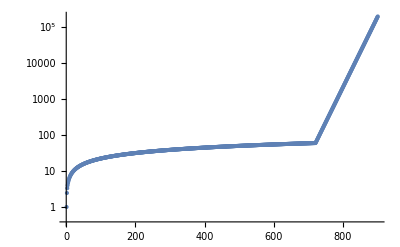

```mathematica
ListLogPlot[CombinedaList]
```

#### Aliases for data

```mathematica
δPowerSpectrumList1=δPowerSpectrumList;
φPlusPowerSpectrumList1=φPlusPowerSpectrumList;
setup1=setup;
```

```mathematica
δPowerSpectrumList2=δPowerSpectrumList;
φPlusPowerSpectrumList2=φPlusPowerSpectrumList;
setup2=setup;
```

```mathematica
δPowerSpectrumList3=δPowerSpectrumList;
φPlusPowerSpectrumList3=φPlusPowerSpectrumList;
setup3=setup;
```

```mathematica
δPowerSpectrumListApproximate1=δPowerSpectrumList;
φPlusPowerSpectrumListApproximate1=φPlusPowerSpectrumList;
setupApproximate1=setup;
```

```mathematica
δPowerSpectrumListApproximate2=δPowerSpectrumList;
φPlusPowerSpectrumListApproximate2=φPlusPowerSpectrumList;
setupApproximate2=setup;
```

#### Plot power spectra

```mathematica
(*powerSpectrumListForPlotting=δPowerSpectrumList384CPU[[{1,3}]]~Join~δPowerSpectrumList384[[{3}]];*)
powerSpectrumListForPlotting=(#[[-1]]&)/@{δPowerSpectrumList,δPowerSpectrum2List};
```

```mathematica
powerSpectrumListForPlotting=(#[[10]]&)/@{(*φPlusPowerSpectrumList1,*)φPlusPowerSpectrumListApproximate1,φPlusPowerSpectrumListApproximate2};
```

```mathematica
indices={1}(*Range[1,numSnapshots,300]*);
powerSpectrumListForPlotting=δPowerSpectrumList[[indices]];
```

```mathematica
freeStreamingPlot=Block[{kSpectrumPointsAll=getIntermediary[setup,"kSpectrumPoints"],epilog,kastLine,amLine,kPsiLine,aHLine,paramText},
kastLine={Red,Thickness[0.003],Line[Log@{{setup["k_ast"],10^-20},{setup["k_ast"],10^10}}],
Text[Style["k_*",{FontFamily->fontfam,FontSize->24}],Log@{0.9setup["k_ast"],10^0.5},{1,0}]};
kPsiLine={Blue,Thickness[0.003],Line[Log@{{setup["k_Psi"],10^-20},{setup["k_Psi"],10^10}}],
Text[Style["SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"Φ\"]",{FontFamily->fontfam,FontSize->24}],Log@{0.9setup["k_Psi"],10^0.5},{1,0}]};
amLine={Purple,Thickness[0.003],Line[Log@{{setup["a1"]setup["m"],10^-20},{setup["a1"]setup["m"],10^10}}],
Text[Style["a_im",{FontFamily->fontfam,FontSize->24}],Log@{0.9setup["a1"]setup["m"],10^0.5},{1,0}]};
aHLine={Cyan,Thickness[0.003],Line[Log@{{setup["a1"]setup["H1"],10^-20},{setup["a1"]setup["H1"],10^10}}],
Text[Style["a_iH_i",{FontFamily->fontfam,FontSize->24}],Log@{0.9setup["a1"]setup["H1"],10^0.7},{1,0}]};
paramText={Black,
Text[Style["k_*/a_i_= "~~ToString[setup["k_ast"]/setup["m"]]~~"m",{FontFamily->fontfam,FontSize->24}],Scaled[{0.95,0.9}],{1,0}],
Text[Style["H_i= "~~ToString[setup["H1"]/setup["m"]]~~"m",{FontFamily->fontfam,FontSize->24}],Scaled[{0.95,0.8}],{1,0}],
Text[Style["k_Ψ/a_i_= "~~ToString[setup["k_Psi"]/setup["m"]]~~"m",{FontFamily->fontfam,FontSize->24}],Scaled[{0.95,0.7}],{1,0}],
Text[Style["a_f/a_i_= "~~ToString[aList[[-1]]/aList[[1]]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.95,0.6}],{1,0}]
};
epilog={(*kastLine,amLine,aHLine,*)paramText};
ListLogLogPlot[powerSpectrumListForPlotting,
PlotLegends->Placed[LineLegend[mtLegendList[[indices]](*{"GPU code","CPU code"}*),LegendMargins->0,LegendMarkerSize->10,LabelStyle->12],{Left,Top}],
PlotRange->(*{{0.1,0.2},{0.005,0.02}}*){{#[[1]],#[[2]]}&@MinMax[kSpectrumPointsAll],{10^-4,10^1}},
ImageSize->Full,
Joined->True,
Frame->True,
FrameLabel->{Style["k/m",24],Style[StringTemplate["k^(`a`)P_(`b`)/(2π^2)"][<|"a"->3,"b"->"δ"|>],24]},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
Epilog->epilog
]
];
```

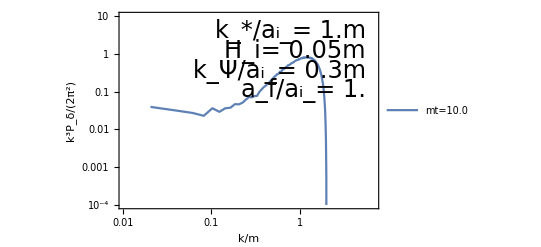

```mathematica
freeStreamingPlot
```

```mathematica
(*Export[NotebookDirectory[]<>"../../Plots/binning_comparison_2.pdf",freeStreamingPlot]*)
```

```mathematica
(*antiDeriv=∫√(q^2/a^2+m^2)ⅆa/a^-1*)
```

```mathematica
(*(antiDeriv/.{a->af})-(antiDeriv/.{a->ai})//ReplaceAll[ai->x af]//Series[#,{x,0,0}]&//Simplify[#,Assumptions->{ai>0,af>0,m>0,q>0,x>0}]&//Normal//FullSimplify*)
```

```mathematica
√((setup["t_start"]+numSnapshots*setup["t_interval"])/setup["t_start"])
```

45.6066

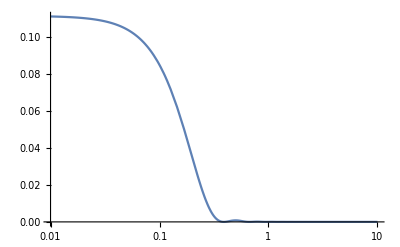

```mathematica
LogLinearPlot[Evaluate[((Sin[φ]-φ Cos[φ])/φ^3)^2/.φ->(k η)/(√3)/.η->1/0.05],{k,10^-2,10},PlotRange->Full]
```

```mathematica
Log[0.4/((2π)/setup["L"])]
```

2.97333

```mathematica
ωη=k/(setup["a1"] setup["H1"]/43)/√3/.k->0.02
(Sin[ωη]-ωη Cos[ωη])/ωη^3
```

1.48956

0.264999

```mathematica
timeUsed=FileDate[dir<>StringTemplate["rho_spectrum_``.dat"][numSnapshots-1]]-FileDate[dir<>"param.dat"]
UnitConvert[timeUsed/((setup["t_end"]-setup["t_start"])/setup["delta_t"]),"s"]
```

2.32694 h

UnitConvert[Missing[KeyAbsent,delta_t] (0.000193912 h),s]

#### Fiting for kfs

```mathematica
dat=δPowerSpectrum2List[[-600,1;;42]];
```

```mathematica
func=afs Exp[-k^2/kfs^2]+aIso k^3;
fit=FindFit[dat,{func,{aIso>0,afs>0,kfs>0}},{afs,kfs,aIso},k,Method->NMinimize]
```

{afs→0.0993859,kfs→0.0506194,aIso→2.00058}

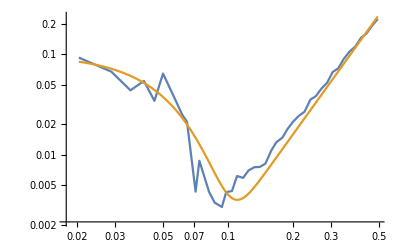

```mathematica
{kmin,kmax}=datᵀ[[1]]//MinMax;
fitted=Table[{k,func/.fit},{k,Subdivide[kmin,kmax,1000]}];
(*fitted2=Table[{k,func2/.fit2},{k,Subdivide[kmin,kmax,1000]}];*)
ListLogLogPlot[{dat,fitted},Joined->True]
```

```mathematica
getFit[dat_]:=Module[{func,fit},
func=afs Exp[-k^2/kfs^2]+aIso k^3;
fit=FindFit[dat,{func,{afs>0,kfs>0,aIso>0}},{afs,kfs,aIso},k,Method->NMinimize];
fit
];
```

```mathematica
kfs/.getFit[dat]
```

0.0506194

```mathematica
kfs/.getFit/@δPowerSpectrum2List[[-1;;-1,1;;42]]
```

{0.0358116}

```mathematica
fitIndices=Range[-600,-1];
fits=getFit/@δPowerSpectrum2List[[fitIndices,1;;42]];
```

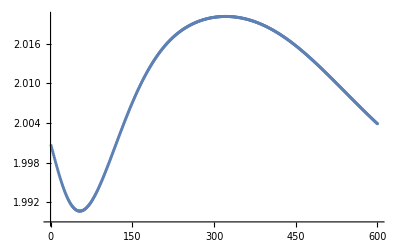

```mathematica
aIso/.fits//ListPlot
```

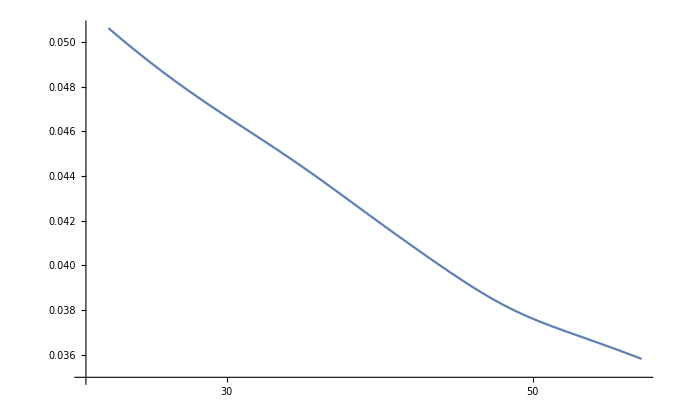

```mathematica
{aList[[fitIndices]],kfs/.fits}ᵀ//ListLogLinearPlot[#,Joined->True]&
```

#### Density perturbation versus time (new)

```mathematica
(*getIntermediary[setup,"multiplicityList"]*)
```

```mathematica
argMax[l_]:={#,Position[l,#,1][[1]]}&@Max[l]
```

```mathematica
argMax[δSpectrumList[[All,14]]]
```

{4.12831×10^12,{12}}

```mathematica
idx=27;
Position[δSpectrumList[[All,idx]],Max[δSpectrumList[[All,idx]]],1][[1,1]]
```

5

```mathematica
f=Interpolation[{aList[[{3,4,5,6,7}]],δSpectrumList[[{3,4,5,6,7},27]]}ᵀ,InterpolationOrder->3,Method->"Spline"];
```

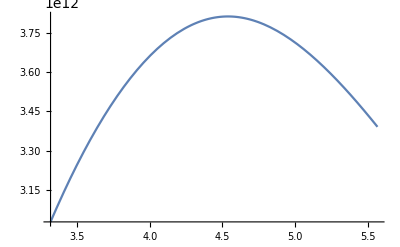

```mathematica
Plot[f[x],{x,aList[[3]],aList[[7]]}]
```

```mathematica
AnnotationKeys[f]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}

```mathematica
AnnotationValue[f,"InterpolationMethod"]
```

BSpline

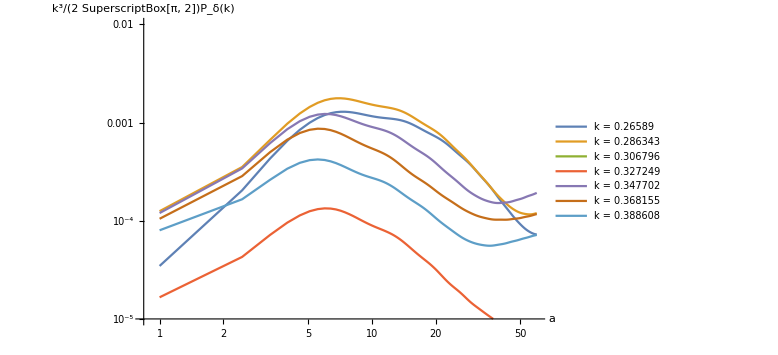

```mathematica
kIndices={14,15,16,17,18,19,20};
δVersusTime=Table[{aList,(*(δSpectrumList[[1,idx]])^-1*)δSpectrumList[[All,idx]]/setup["N"]^6}ᵀ,{idx,kIndices}];
ListLogLogPlot[δVersusTime,AxesLabel->{"a",(*"|δ_k^2|"*)"k^3/(2 SuperscriptBox[π, 2])P_δ(k)"},
PlotRange->{All,{10^-5,10^-2}},
(*Epilog->{Text[Style["k = "~~ToString[δPowerSpectrumList[[1,idx,1]]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.95,0.2}],{1,0}]},*)
PlotLegends->Table["k = "~~ToString[δPowerSpectrumList[[1,idx,1]]],{idx,kIndices}],
ImageSize->Large,Joined->True]
```

#### Density perturbation versus time

```mathematica
δPowerSpectrumList[[1,2,1]]
```

0.0204531

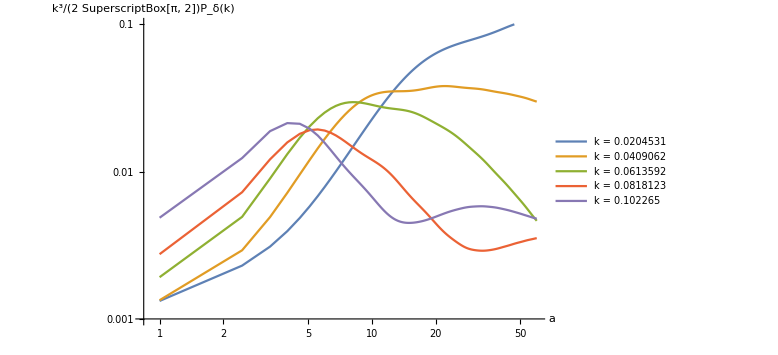

```mathematica
kIndices={2,3,4,5,6};
δVersusTime=Table[{aList,(*(δPowerSpectrumList[[All,idx,1]]^3/(2 π^2))^-1*)δPowerSpectrumList[[All,idx,2]]}ᵀ,{idx,kIndices}];
ListLogLogPlot[δVersusTime,AxesLabel->{"a",(*"|δ_k^2|"*)"k^3/(2 SuperscriptBox[π, 2])P_δ(k)"},
PlotRange->{All,{10^-3,10^-1}},
(*Epilog->{Text[Style["k = "~~ToString[δPowerSpectrumList[[1,idx,1]]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.95,0.2}],{1,0}]},*)
PlotLegends->Table["k = "~~ToString[δPowerSpectrumList[[1,idx,1]]],{idx,kIndices}],
ImageSize->Large,Joined->True]
```

#### Animation for φ, δ

```mathematica
AbsoluteTiming[φAnimation=
Block[{kSpectrumPointsAll=getIntermediary[setup,"kSpectrumPoints"],legends},
legends={"Initial","Current"};
Table[
ListLogLogPlot[{φPlusPowerSpectrumList[[1]],φPlusPowerSpectrumList[[i]]},
PlotRange->{All,{10^-6,10^1}},
PlotStyle->{Gray,Black},
ImageSize->Large,
Epilog->{
Text[Style[mtLegendList[[i]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.95}],{-1,0}]
},
Joined->True,
Frame->True,
FrameLabel->{Style["k/m",24],Style[StringTemplate["k^(`a`)P_(`b`)/(2π^2)"][<|"a"->3,"b"->"φ"|>],24]},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLegends->Placed[LineLegend[legends,LegendMargins->0,LegendMarkerSize->10,LabelStyle->12],{Right,Top}]
]//Rasterize,{i,Range[1,2]}]
];]
```

{0.27938,Null}

```mathematica
Export[NotebookDirectory[]<>"Plots/varphi_6_sqrt.mov",φAnimation,VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming
```

{2.1724,/home/hypermania/Dropbox/Research/FreeStreamingULDM/Plots/varphi_6_sqrt.mov}

Compute free-streaming scale.

```mathematica
kfsList=Table[Block[{φPlusPowerSpectrum=φPlusPowerSpectrumList[[i]],logLinearSpectrum,qfsList,qfsInverse,at=aList[[i]],a1=setup["a1"],H1=setup["H1"],m=setup["m"],integrandFunc1,integrandFunc2,lnkMin,lnkMax,kfsInverseSqr},
qfsInverse=(q ArcSinh[(at m)/q])/(a1^2 H1 m)-(q ArcSinh[(a1 m)/q])/(a1^2 H1 m);
logLinearSpectrum={Log[#[[1]]],#[[2]]}&/@φPlusPowerSpectrum[[2;;-1]];
integrandFunc1=Interpolation[({#[[1]],(qfsInverse/.q->Exp[#[[1]]])^2#[[2]]}&/@logLinearSpectrum)];
integrandFunc2=Interpolation[logLinearSpectrum];
lnkMin=AnnotationValue[integrandFunc2,"Grid"][[2,1]];
lnkMax=AnnotationValue[integrandFunc2,"Grid"][[-1,1]];
kfsInverseSqr=NIntegrate[integrandFunc1[lnk],{lnk,lnkMin,lnkMax}]/NIntegrate[integrandFunc2[lnk],{lnk,lnkMin,lnkMax}];
(*Print["t=",tList[[i]]];
Print["qfs=",((q ArcSinh[(at m)/q])/(a1^2 H1 m)-(q ArcSinh[(a1 m)/q])/(a1^2 H1 m))^-1/.{q->setup["k_ast"],at->aList[[i]]}];
Print["kfs=",kfsInverseSqr^(-1/2)];
{integrandFunc1,integrandFunc2,kfsInverseSqr}*)
kfsInverseSqr^(-1/2)
],{i,2,numSnapshots}];
```

```mathematica
(*kfsListNew=kfsList;
ListLogLogPlot[{{aList[[2;;-1]],kfsListOld}ᵀ,{aList[[2;;-1]],kfsListNew}ᵀ},Joined->True]*)
```

```mathematica
(*lnkMinTemp=AnnotationValue[result[[1,2]],"Grid"][[2,1]]
lnkMaxTemp=AnnotationValue[result[[1,2]],"Grid"][[-1,1]]
LogPlot[{result[[1,1]][lnk],result[[1,2]][lnk]},{lnk,lnkMinTemp,lnkMaxTemp},ImageSize->Large,PlotLegends->{"Numerator Integrand","Denominator Integrand"}]*)
```

```mathematica
AbsoluteTiming[δAnimation=
Block[{kSpectrumPointsAll=getIntermediary[setup,"kSpectrumPoints"],legends,kfs,kfsLine,a1=setup["a1"],H1=setup["H1"],m=setup["m"],atHt,atHtLine},
legends={"Initial","Current"};
Table[
(*kfs=kfsList[[i-1]];
kfsLine=If[i>=2,{Red,Thickness[0.003],Line[Log@{{kfs,10^-20},{kfs,10^10}}],
Text[Style["SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"fs\"]",{FontFamily->fontfam,FontSize->24}],Log@{0.9kfs,10^0.5},{1,0}]},{}];*)
atHt=aList[[i]]HList[[i]];
atHtLine={Blue,Thickness[0.003],Line[Log@{{atHt,10^-20},{atHt,10^10}}],
Text[Style["aH",{FontFamily->fontfam,FontSize->24}],Log@{0.9atHt,10^0.5},{1,0}]};
ListLogLogPlot[(*{δPowerSpectrumList[[1]],δPowerSpectrumList[[i]]}*){δPowerSpectrum2List[[1]],δPowerSpectrum2List[[i]]},
(*PlotRange->{{10^-3,4},{10^-4,10^1}},*)
PlotRange->{{10^-3,0.5},{10^-4,10^1}},
PlotStyle->{Gray,Orange},
ImageSize->Large,
Epilog->{
(*Text[Style["σ_Ψ="~~ToString[setup["Psi_std_dev"]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.85}],{-1,0}],*)
Text[Style[mtLegendList[[i]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.95}],{-1,0}],
(*kfsLine,*)
(*atHtLine*)
},
Joined->True,
Frame->True,
FrameLabel->{Style["k/a_im",24],Style[StringTemplate["k^(`a`)P_(`b`)/(2π^2)"][<|"a"->3,"b"->"δ"|>],24]},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLegends->Placed[LineLegend[legends,LegendMargins->0,LegendMarkerSize->10,LabelStyle->12],{Right,Top}]
](*//Rasterize*),{i,(*Range[1,Length@δPowerSpectrum2List]*){1,Length@δPowerSpectrum2List}}]
];]
```

{0.029904,Null}

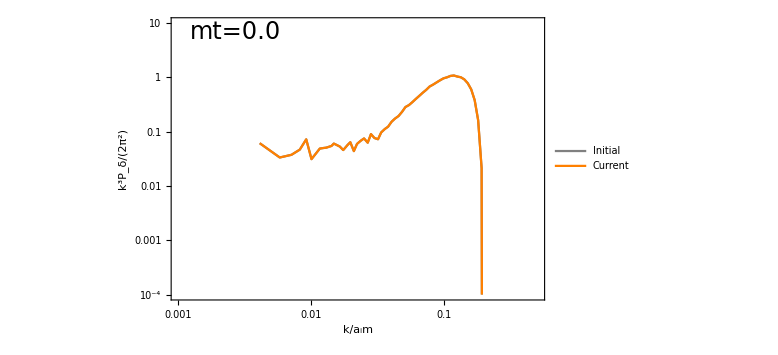

```mathematica
δAnimation[[1]]
```

```mathematica
(*CombinedmtLegendList[[700;;800]]*)
```

```mathematica
(*GraphicsRow[δAnimation,ImageSize->Full]*)
```

```mathematica
Export[NotebookDirectory[]<>"../../Plots/delta_growth_and_fs_2_with_wkb.mov",δAnimation,VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming
```

{3.17544,/home/hypermania/Dropbox/Research/FreeStreamingULDM/Numerics/Project/../../Plots/delta_growth_and_fs_2_with_wkb.mov}

```mathematica
(*Export[NotebookDirectory[]<>"../../Plots/delta_without_gravity_2.pdf",δAnimation[[2]],VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming*)
```

#### Animation for comparing different Ψ amplitudes

```mathematica
AbsoluteTiming[δAnimation=
Block[{kSpectrumPointsAll=getIntermediary[setup,"kSpectrumPoints"],legends,kfs,kfsLine,a1=setup["a1"],H1=setup["H1"],m=setup["m"],atHt,atHtLine},
(*legends={"Initial","Current"};*)
legends=Table[StringTemplate["σ_Ψ=``"][s["Psi_std_dev"]],{s,{setup1,setup2,setup3}}];
Table[
atHt=aList[[i]]HList[[i]];
atHtLine={Blue,Thickness[0.003],Line[Log@{{atHt,10^-20},{atHt,10^10}}],
Text[Style["aH",{FontFamily->fontfam,FontSize->24}],Log@{0.9atHt,10^0.5},{1,0}]};
ListLogLogPlot[{δPowerSpectrumList1[[i]],δPowerSpectrumList2[[i]],δPowerSpectrumList3[[i]]},
PlotRange->{All,{10^-4,10^1}(*{10^-7,10^-3}*)},
(*PlotStyle->{Gray,Orange},*)
ImageSize->Large,
Epilog->{
(*Text[Style["σ_Ψ="~~ToString[setup["Psi_std_dev"]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.85}],{-1,0}],*)
Text[Style[mtLegendList[[i]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.95}],{-1,0}],
atHtLine
},
Joined->True,
Frame->True,
FrameLabel->{Style["k/m",24],Style[StringTemplate["k^(`a`)P_(`b`)/(2π^2)"][<|"a"->3,"b"->"δ"|>],24]},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLegends->Placed[LineLegend[legends,LegendMargins->0,LegendMarkerSize->10,LabelStyle->12],{Right,Top}]
]//Rasterize,{i,Range[1,numSnapshots]}]
];]
```

{158.304,Null}

```mathematica
δAnimation[[1]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../../Plots/delta_growth_and_fs_comparison.mov",δAnimation,VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

{3.54618,/home/hypermania/Dropbox/Research/FreeStreamingULDM/Numerics/Project/../../Plots/delta_growth_and_fs_comparison.mov}

```mathematica
AbsoluteTiming[φAnimation=
Block[{kSpectrumPointsAll=getIntermediary[setup,"kSpectrumPoints"],legends,kfs,kfsLine,a1=setup["a1"],H1=setup["H1"],m=setup["m"],atHt,atHtLine},
(*legends={"Initial","Current"};*)
legends=Table[StringTemplate["σ_Ψ=``"][s["Psi_std_dev"]],{s,{setup1,setup2,setup3}}];
Table[
atHt=aList[[i]]HList[[i]];
atHtLine={Blue,Thickness[0.003],Line[Log@{{atHt,10^-20},{atHt,10^10}}],
Text[Style["aH",{FontFamily->fontfam,FontSize->24}],Log@{0.9atHt,10^0.5},{1,0}]};
ListLogLogPlot[{φPlusPowerSpectrumList1[[i]],φPlusPowerSpectrumList2[[i]],φPlusPowerSpectrumList3[[i]]},
PlotRange->{All,{10^-18,10^1}(*{10^-7,10^-3}*)},
(*PlotStyle->{Gray,Orange},*)
ImageSize->Large,
Epilog->{
(*Text[Style["σ_Ψ="~~ToString[setup["Psi_std_dev"]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.85}],{-1,0}],*)
Text[Style[mtLegendList[[i]],{FontFamily->fontfam,FontSize->24}],Scaled[{0.05,0.95}],{-1,0}],
atHtLine
},
Joined->True,
Frame->True,
FrameLabel->{Style["k/m",24],Style[StringTemplate["k^(`a`)P_(`b`)/(2π^2)"][<|"a"->3,"b"->"φ"|>],24]},
FrameStyle->Directive[{Black,FontFamily->fontfam,FontSize->18,Thickness[framethick]}],
PlotLegends->Placed[LineLegend[legends,LegendMargins->0,LegendMarkerSize->10,LabelStyle->12],{Right,Top}]
]//Rasterize,{i,Range[1,numSnapshots]}]
];]
```

{120.672,Null}

```mathematica
φAnimation[[1]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../../Plots/varphi_growth_and_fs_comparison.mov",φAnimation,VideoEncoding->"MPEG2VIDEO"]//AbsoluteTiming
```

{2.00339,/home/hypermania/Dropbox/Research/FreeStreamingULDM/Numerics/Project/../../Plots/varphi_growth_and_fs_comparison.mov}

```mathematica
{0.11827 ,0.131918, 0.145565}//Differences
```

{0.013648,0.013647}